## ^183Au - Wobbling analysis

### Analytical formulae

```mathematica
I0=4.5;
j=4.5;
IF[MOI_]:=1/(2*MOI);
RAD[angle_]:=angle*π/180;
HMin[I_,j_,A1_,A2_,A3_,V_,γ_]:=(A2+A3)(I+j)/2+A1*(I-j)^2-V*(2j-1)/(j+1)*Sin[γ+π/6];
B1[I_,j_,A1_,A2_,A3_,V_,γ_]:=-1*(((2I-1)*(A3-A1)+2j*A1)*((2I-1)*(A2-A1)+2j*A1)+8*A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]))*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2Sqrt[3]Sin[γ]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=((((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]))-4I*j*A3^2)*(((2I-1)*(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2Sqrt[3]Sin[γ])-4I*j*A2^2));
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=Sqrt[1/2(-B1[I,j,A1,A2,A3,V,γ]-Sqrt[B1[I,j,A1,A2,A3,V,γ]^2-4*C1[I,j,A1,A2,A3,V,γ]])];
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=Sqrt[1/2(-B1[I,j,A1,A2,A3,V,γ]+Sqrt[B1[I,j,A1,A2,A3,V,γ]^2-4*C1[I,j,A1,A2,A3,V,γ]])];
Energy[nw1_,nw2_,I_,j_,A1_,A2_,A3_,V_,γ_]:=HMin[I,j,A1,A2,A3,V,γ]+Omega1[I,j,A1,A2,A3,V,γ](nw1+1/2)+Omega2[I,j,A1,A2,A3,V,γ](nw2+1/2);
ExcEn[nw1_,nw2_,I_,A1_,A2_,A3_,V_,γ_]:=Energy[nw1,nw2,I,j,A1,A2,A3,V,γ]-Energy[0,0,I0,j,A1,A2,A3,V,γ];
band1[I_,I1_,I2_,I3_,V_,γ_]:=ExcEn[0,0,I,IF[I1],IF[I2],IF[I3],V,RAD[γ]];
band2[I_,I1_,I2_,I3_,V_,γ_]:=ExcEn[1,0,I,IF[I1],IF[I2],IF[I3],V,RAD[γ]];
```

#### Experimental data

```mathematica
spin1=Table[N[i],{i,9/2,53/2,2}];
spin2=Table[N[i],{i,19/2,51/2,2}];
yrast=N[{12.78,232,566,990,1492,2063,2690,3358,4050,4760,5497,6242}/1000];
tw1=N[{1056,1488,1987,2540,3148,3796,4457,5133,5912}/1000];
bandHead=yrast[[1]];
yrast=Table[yrast[[i]]-bandHead,{i,1,Length[yrast]}];
tw1=Table[tw1[[i]]-bandHead,{i,1,Length[tw1]}];
```

#### Fitting parameters - numerical results from Mathematica

```mathematica
params={86.7116832,10.3061754,4.3612584,0.1747387,21.23393895};
rms=0.07927540393557526;
```

## Wobbling frequencies

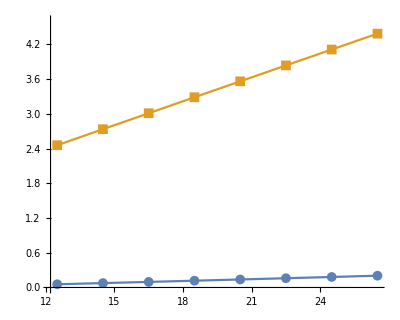

```mathematica
omega1Plot=Table[{spin,Omega1[spin,j,IF[params[[1]]],IF[params[[2]]],IF[params[[3]]],params[[4]],RAD[params[[5]]]]},{spin,25/2,55/2,2}];
omega2Plot=Table[{spin,Omega2[spin,j,IF[params[[1]]],IF[params[[2]]],IF[params[[3]]],params[[4]],RAD[params[[5]]]]},{spin,25/2,55/2,2}];
(*Show[ListPlot[{omega1Plot},Joined->True,PlotMarkers->{Automatic, Medium}],PlotRange->Full]
Show[ListPlot[{omega2Plot},Joined->True,PlotMarkers->{Automatic, Medium}],PlotRange->Full]
*)
Show[ListPlot[{omega1Plot,omega2Plot},Joined->True,PlotMarkers->{Automatic, Medium},PlotRange->{0,4.6},AspectRatio->0.8]]
```

```mathematica
Print[#]&[Table[omega1Plot[[i,2]],{i,1,Length[omega1Plot]}]]
```

{0.0120952,0.00081192,0.0180452,0.0362675,0.0555502,0.0755746,0.0961381,0.117107,0.138389,0.159917,0.181644,0.203533}

## Wobbling energy - E_wobb

```mathematica
yrastTh=Table[band1[spin1[[i]],params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]],{i,1,Length[spin1]}];
tw1Th=Table[band2[spin2[[i]],params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]],{i,1,Length[spin2]}];
```

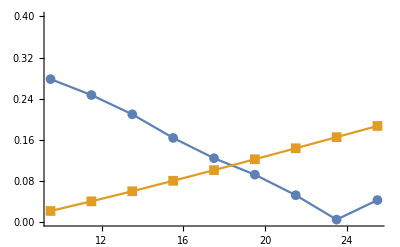

```mathematica
ewobExp=Table[{spin2[[i]],tw1[[i]]-(yrast[[i+2]]+yrast[[i+3]])/2},{i,1,Length[tw1]}];
ewobTh=Table[{spin2[[i]],tw1Th[[i]]-(yrastTh[[i+2]]+yrastTh[[i+3]])/2},{i,1,Length[tw1Th]}];
Show[ListPlot[{ewobExp,ewobTh},Joined->True,PlotMarkers->{Automatic, Medium}],PlotRange->{0,0.4}]
```

## Rotational frequency

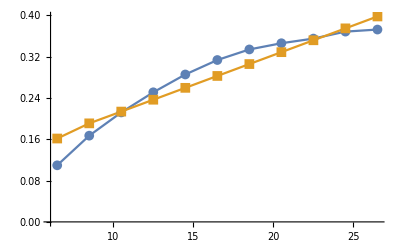

```mathematica
homega1Exp=Table[{spin1[[i]],(yrast[[i]]-yrast[[i-1]])/2},{i,2,Length[yrast]}];
homega1Th=Table[{spin1[[i]],(yrastTh[[i]]-yrastTh[[i-1]])/2},{i,2,Length[yrast]}];
ListPlot[{homega1Exp,homega1Th},Joined->True,PlotMarkers->{Automatic, Medium}]
```

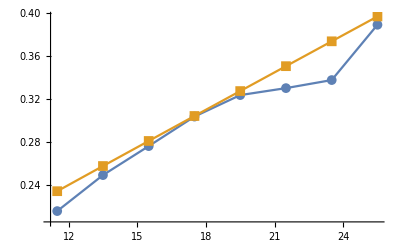

```mathematica
homega2Exp=Table[{spin2[[i]],(tw1[[i]]-tw1[[i-1]])/2},{i,2,Length[tw1]}];
homega2Th=Table[{spin2[[i]],(tw1Th[[i]]-tw1Th[[i-1]])/2},{i,2,Length[tw1Th]}];
ListPlot[{homega2Exp,homega2Th},Joined->True,PlotMarkers->{Automatic, Medium}]
```